# Lecture 31: SVD Algorithms

Time to learn how to compute the SVD A=U.Σ.V^*.  Perhaps not surprisingly, SVD algorithms look quite a bit like eigenvalue algorithms.

## Eigenvalues of A^*.A

If A=U.Σ.V^* is the SVD then A^*.A=(U.Σ.V^*)^*.U.Σ.V^*=V.Σ^*.U^*.U.Σ.V^*=V.Σ^*.Σ.V^* since U is unitary.  More over, since Σ is real we wind up with A^*.A=V.Σ^2.V^*.  We can compute the Hermitian eigenvalue problem A^*.A=V.Λ.V^* then compute 
Σ as the diagonal matrix of the positive square roots of Λ and compute U from U.Σ=A.V.  The problem with this (or similarly computing with A.A^*) is that we know this problem (just like the normal equations) is more sensitive to perturbations than it needs to be.   The fundamental problem is the we formed the product. The stability problem is most extreme for the smaller singular values.

Just another reminder why forming A.A^* is a bad idea. I am going to make a matrix with a broad range of singular values.  The BuiltIn SVD does almost OK with the following

```mathematica
{m,n}={23,12};
σsIn=Sort[Table[10.0^(i-8),{i,Min[m,n]}]];
S=SparseArray[Band[{1,1}]->σsIn,{m,n}];
U=Orthogonalize[RandomReal[{-1,1},{m,m}]];
V=Orthogonalize[RandomReal[{-1,1},{n,n}]];
A=U.S.Vᵀ;
σsBIOut=Sort[SingularValueList[A,Tolerance->0]];
(σsBIOut-σsIn)/σsIn
```

{4.4541×10^-7,-1.97928×10^-9,7.07868×10^-9,-1.61789×10^-9,-1.27405×10^-10,-7.60156×10^-13,5.77594×10^-13,2.13163×10^-14,1.26121×10^-14,8.52651×10^-16,-4.54747×10^-16,1.81899×10^-16}

The “normal” A.A^* computation is completely broken!

```mathematica
Eigenvalues[A.ConjugateTranspose[A]]
```

{1.×10^8,1.×10^6,10000.,100.,1.,0.01,0.0000999991,9.99573×10^-7,-1.56646×10^-8,1.15295×10^-8,7.31924×10^-9,2.78467×10^-9,-1.90375×10^-9,1.5818×10^-9,-1.42745×10^-9,-9.65521×10^-10,6.87106×10^-10,-6.24362×10^-10,-3.76151×10^-10,2.73945×10^-10,-2.22422×10^-10,1.54583×10^-10,-2.10705×10^-11}

## Eigenvalues of H=(0 | A^* A | 0)

A direct computation shows that if A=U.Σ.V^* then 
	(0 | A^*
A | 0).(V | V
U | -U)=(A^*.U | -A^*.U
A.V | A.V)
Since A=U.Σ.V^* we have A.V=U.Σ.V^*.V=U.Σ.  
Since A^*=V.Σ.U^* we have that A^*.U=V.Σ.U^*.U=V.Σ. 
So
	(0 | A^*
A | 0).(V | V
U | -U)=(V.Σ | -V.Σ
U.Σ | U.Σ)=(V | V
U | -U).(Σ | 0
0 | -Σ).
In words, the eigen values of the big Hermitian matrix in the heading are the ± the singular values. The singular vectors are in the eigenvectors.

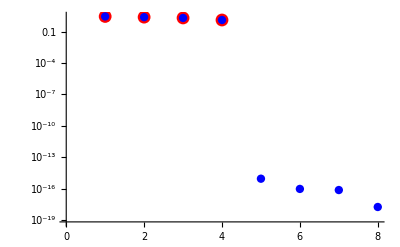

```mathematica
{m,n}={12,4};
A=RandomReal[{-1,1},{m,n}];
H=ArrayFlatten[({{0, ConjugateTranspose[A]}, {A, 0}})];
MatrixPlot[H];
{λ,V}=Eigensystem[H];
σ=SingularValueList[A];
ListLogPlot[{σ,Select[λ,Positive]},GridLines->Automatic,
PlotStyle->{
Directive[Red,PointSize[0.023]],
Directive[Blue, PointSize[0.015]]}]
```

This stable algorithm is what computes 99.999% of all SVDs in the world.  It is sneaky because it does not actually need to make the big H matrix! Just like for eigenvalues there is a preliminary reduction.

For singular values, we can get to an upper bi-diagonal matrix! The bi-diagonal form is then iteratively reduced to a diagonal form.  If you only want singular values you do not need to keep the rotations

### Bi-diagonalization: Golub Kahan

The plan is to use Householder operations on the left and right to rotate the matrix to an upper bi-diagonal form. I am going to call the right rotations U and the left rotations V.

#### Preliminary Script.

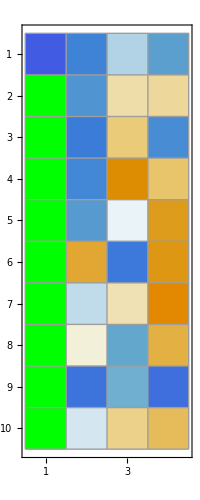

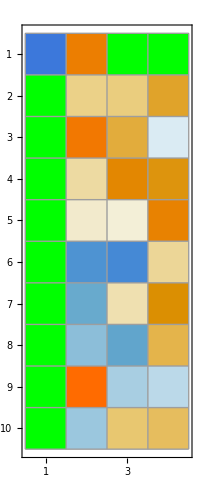

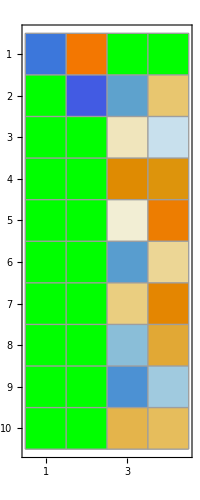

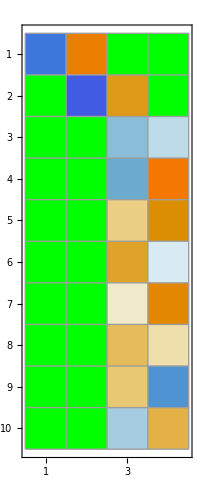

```mathematica
SetOptions[MatrixPlot,ColorRules->{0->Green}, Mesh->All];
{m,n}={10,4};
A=A0=RandomReal[{-1,1},{m,n}];
U=HouseMat[A⟦1;;m,1⟧];
A⟦1;;m,1;;n⟧=Chop[U.A⟦1;;m,1;;n⟧];
MatrixPlot[A]
V=HouseMat[A⟦1,2;;n⟧];
A⟦1;;m,2;;n⟧=Chop[A⟦1;;m,2;;n⟧.V];
MatrixPlot[A]
U=HouseMat[A⟦2;;m,2⟧];
A⟦2;;m,2;;n⟧=Chop[U.A⟦2;;m,2;;n⟧];
MatrixPlot[A]
V=HouseMat[A⟦2,3;;n⟧];
A⟦2;;m,3;;n⟧=Chop[A⟦2;;m,3;;n⟧.V];
MatrixPlot[A]
```

I guess we should check that the singular values are being preserved.

```mathematica
TableForm[Map[SingularValueList,{A,A0}]]
```

2.32707 | 1.76777 | 1.31506 | 0.927963
2.32707 | 1.76777 | 1.31506 | 0.927963

#### Function Golub-Kahan

```mathematica
GKBiDiagonalization[AIn_]:= Module[{A=AIn,m,n,U,V},
{m,n}=Dimensions[AIn];
(* Assuming Tall Skiinny m≥n *) 
Do[
U=HouseMat[A⟦k;;m,k⟧];
A⟦k;;m,k;;n⟧=Chop[U.A⟦k;;m,k;;n⟧];
V=HouseMat[A⟦k,k+1;;n⟧];
A⟦k;;m,k+1;;n⟧=Chop[A⟦k;;m,k+1;;n⟧.V],
{k, 1,n-1}];
(* Tidy up the Last Column *)
U=HouseMat[A⟦n;;m,n⟧];
A⟦n;;m,n;;n⟧=Chop[U.A⟦n;;m,n;;n⟧];
A]
```

```mathematica
{m,n}={23,7};
A=RandomReal[{-1,1},{m,n}];
B=GKBiDiagonalization[A];
Map[SingularValueList,{A,B}]
MatrixPlot[B];
```

{{3.89304,3.83097,2.88306,2.56771,2.35186,1.60785,1.02162},{3.89304,3.83097,2.88306,2.56771,2.35186,1.60785,1.02162}}

### Bi-diagonalization: Lawson Hanson Chan

An alternative would be to Upper Triangularize using QR then Bidiaogonalize the remaining Upper Triangle just like above.

#### Function Lawson-Hanson-Chan

```mathematica
LHCBiDiagonalization[A_]:= Module[{R,m,n,U,V},
{m,n}=Dimensions[A];
(* Assuming Tall Skinny m≥n *)
R=QRDecomposition[A]⟦2⟧;
R=GKBiDiagonalization[R]; 
ArrayFlatten[ ({{R}, {ConstantArray[0,{m-n,n}]}})]
]
```

{{4.12261,3.45262,3.01417,2.45676,2.26417,2.13711,1.57869},{4.12261,3.45262,3.01417,2.45676,2.26417,2.13711,1.57869}}

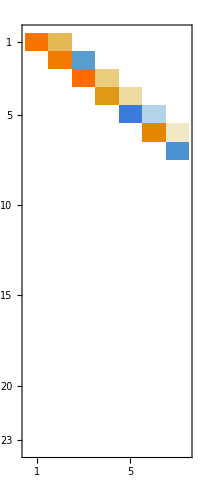

```mathematica
A=RandomReal[{-1,1},{m,n}];
B=LHCBiDiagonalization[A];
Map[SingularValueList,{A,B}]
MatrixPlot[B]
```

### Operation Counts and Three Step BiDiagonalization

It turns out that LHC is more work than GK for nearly square matrices. While GK is more work for very tall skinny matrices. So the right thing to do depends on the aspect ration γ=m/n

GK 	~4 m n^2-4/3 n^3=4/3 n^3 (3γ-1)

LHC	~2 m n^2+2 n^3=2 n^3 (γ+1)

To find the crossover point solve 4/3 n^3 (3γ-1)=2n^3(γ+1) for γ.

The crossover point is γ=m/n=5/3: LHC is less work above 5/3 and GK is less work below 5/3.

Just to make it a little more complicated as far as operation counts are concerned

It is always best to do GK at the beginning(the matrix is always effectively very TS there).

The first

4 m n^2-4/3 n

Plot

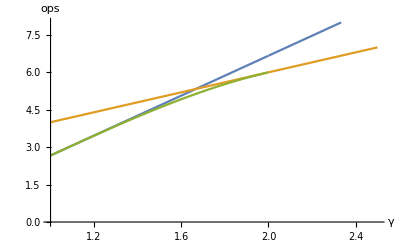

4/3 n^3 (-1+3 γ)

2 n^3 (1+γ)

-2/3 n^3 (1-3 γ-3 γ^2+γ^3)

```mathematica
Plot[ {4/3 (3γ-1),2(γ +1),If[γ<2,2/3 (3 γ+3 γ^2-γ^3-1)]},{γ,1,2.5},
PlotRange->{0,8},
AxesLabel->{"γ","ops"}]
Clear[m,n,γ]
Simplify[(4 m n^2-4/3 n^3)/.m->γ n]
Simplify[(2 m n^2+2 n^3)/.m->γ n]
Simplify[(4 m n^2-4/3 n^3-2/3(m-n)^3)/.m->γ n]
```

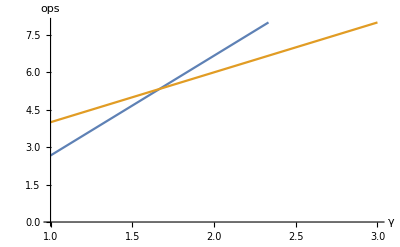

4/3 n^3 (-1+3 γ)

2 n^3 (1+γ)

-2/3 n^3 (1-3 γ-3 γ^2+γ^3)

{{γ→5/3}}

```mathematica
Eq=4 m n^2-4/3 n^3-(2 m n^2+ 2 n^3);
Eq=Simplify[Eq/n^3/.{m->γ n}];
Solve[Eq==0,γ]
```

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}